## Branching Processes

Suppose  that the population size at time 0  is X_0 = 1 and that each member of the population will produce k new offspring with probability P_k and independently of each other. Namely, the number of offspring of each member of the population is a random variable Z with P(Z = k) = P_k. Let X_n  = population size at the n-th generation. This is called a Branching Process.  

Then X_n =  ∑_(i=1)^(X_(n -1)) Z_i, where Z_i  are i.i.d. ~ Z.  Denoting  μ = E[Z]  and  σ^2 = Var[Z]  one has 


                    E[X_n] = μ^n   with   Var[X_n] = n σ^2  when μ = 1     and     Var[X_n]= σ^2μ^(n-1)((μ^n-1)/(μ-1))   when  μ ≠ 1.

Branching processes are studied through the Probability Generating Function (PGF) [similar to the Moment Generating Function (MGF)] of the random variable Z defined by

                     φ(s) = ∑_(k=0)^∞  s^kP_k ,      0 ≤ s ≤ 1

whose properties are as follows:

          φ(0) =  P_0    
          φ'(1) = E[Z] = μ = slope at  s = 1 ,   
          φ(s)  is increasing [ φ'(s) ≥ 0 ] and convex [ φ''(s) ≥ 0]  ,   0 ≤ s ≤ 1

Main question to answer is the probability of population extinction.

THEOREM.  Let  0  <  P_0  < 1 . Then

 ■   If   μ  ≤ 1   then  π_0 = probability of extinction = P( population eventually dies out ) = 1

 ■   If   μ  > 1   then  π_0  is the smallest positive solution to 
  

(*)                                       s  =  φ(s)  ,     0<s≤ 1

     
Furthermore,  π_n = P( population dies out by the n-th generation ) = P( X_n = 0) is a solution to


(**)                                      π_n = ∑_(k=0)^∞  (π_(n-1))^k P_k ,        n  ≥ 1
  

Based on {X_n = 0} ⊂ {X_(n+1) = 0} one has 
 

(***)   p_n = P(population dies out in the n-th generation) = P( X_n = 0 and X_j≠ 0, j = 0, 1, ... , n-1)  = π_n - π_(n-1),  n = 2, 3,... 
 
           p_1 = π_1 = P_0
 , for n = 1
           
 REMARK.  If  P_0 = 0  (i.e., each population member has at least one offspring) then the population will never die out, 
 and therefore the probability of extinction is zero.  If  P_0 = 1 then the population is extinct in the first generation.

EXAMPLE.  In the case of up to 2 offsprings,  φ(s) = P_0 + s P_1 + s^2 P_2.  For  P_0 = P_1 = P_2 = 1/3,  E[Z] = μ = 1 and the probability 
of extinction  π_0 = 1. However, for P_0 = 1/3, P_1 = 2/9, P_2 = 4/9 ,  E[Z] = μ = 10/9 > 1  and therefore  π_0 < 1.  The smallest positive 
solution  to  (*)   is   π_0 = 3/4 as confirmed below.

```mathematica
Clear[s];Solve[s==1/3+ s 2/9+s^2 4/9 ,s]
{{s->3/4},{s->1}}
```

Below are two graphs illustrating the two different cases.

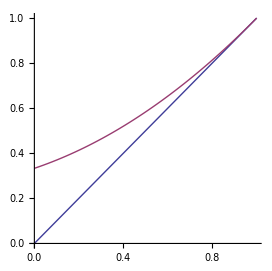

```mathematica
Plot[{s,1/3+1/3s + 1/3s^2},{s,0,1},AspectRatio->Automatic]
```

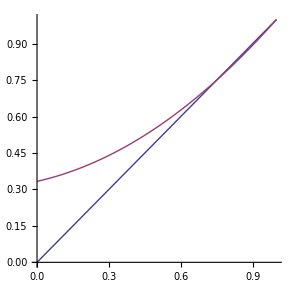

```mathematica
Plot[{s,1/3+2/9s + 4/9s^2},{s,0,1},AspectRatio->Automatic]
```

To find the probability p_5of extinction in the 5-th generation one has to find {π_1, π_2, π_3, π_4, π_5} by solving  (**) recursively 
and then use (***) to find  p_5= π_5 - π_4 by backward substitution.

```mathematica
π1=1/3;
π2=1/3+ π1 2/9+π1^2 4/9 //N
```

0.45679

```mathematica
π3=1/3+ π2 2/9+π2^2 4/9 //N
```

0.527579

```mathematica
π4=1/3+ π3 2/9+π3^2 4/9 //N
```

0.574279

```mathematica
π5=1/3+ π4 2/9+π4^2 4/9 //N
```

0.607527

```mathematica
Subscript[p, 5]=π5-π4//N
```

0.0332479

## Simulation

Below are simulations of the first 5 generations in the case  P_0 = P_1 = P_2 = 1/3, for which E[Z] = μ = 1 and  E[X_5] = μ^5= 1.

The output printed to the screen reads as follows:

1-st element of each list = # members in the population  
2-nd  element of the list = list of  #’s of offspring of each respective member of the population
If population dies out before the predefined NumGenerations, only the history till extinction is printed to the screen

```mathematica
OffspringNumber:=RandomInteger[{0,2}]
x=1;NumGenerations=5;size=0;
Do[If[x>0,a=Table[OffspringNumber,{x}];Print[{x,a}];x=Apply[Plus,a]],{NumGenerations}]
size=size+x;
Print["population size in the ",NumGenerations,"-th generation = ",size]
```

{1,{2}}

{2,{1,1}}

{2,{2,2}}

{4,{2,2,1,0}}

{5,{1,1,2,2,1}}

population size in the 5-th generation = 7

```mathematica
OffspringNumber:=RandomInteger[{0,2}]
x=1;NumGenerations=5;size=0;
Do[If[x>0,a=Table[OffspringNumber,{x}];Print[{x,a}];x=Apply[Plus,a]],{NumGenerations}]
size=size+x;
Print["population size in the ",NumGenerations,"-th generation = ",size]
```

{1,{2}}

{2,{0,1}}

{1,{2}}

{2,{0,0}}

population size in the 5-th generation = 0

Below are couple simulation of the first 10 generations in the case  P_0 = P_1 = P_2 = 1/3, for which E[Z] = μ = 1 and  E X_5 = μ^5 = 1.

```mathematica
OffspringNumber:=RandomInteger[{0,2}]
x=1;NumGenerations=10;size=0;
Do[If[x>0,a=Table[OffspringNumber,{x}];Print[{x,a}];x=Apply[Plus,a]],{NumGenerations}]
size=size+x;
Print["population size in the ",NumGenerations,"-th generation = ",size]
```

{1,{2}}

{2,{2,2}}

{4,{2,2,1,2}}

{7,{1,1,2,2,1,0,2}}

{9,{0,1,2,0,1,2,2,0,0}}

{8,{0,1,0,0,1,2,1,1}}

{6,{2,2,2,0,2,1}}

{9,{1,1,1,0,1,0,1,1,0}}

{6,{2,0,2,0,0,1}}

{5,{0,1,0,2,2}}

population size in the 10-th generation = 5

```mathematica
OffspringNumber:=RandomInteger[{0,2}]
x=1;NumGenerations=10;size=0;
Do[If[x>0,a=Table[OffspringNumber,{x}];Print[{x,a}];x=Apply[Plus,a]],{NumGenerations}]
size=size+x
Print["population size in the ",NumGenerations,"-th generation = ",size]
```

{1,{2}}

{2,{1,1}}

{2,{1,0}}

{1,{2}}

{2,{0,0}}

0

population size in the 10-th generation = 0

To find   π_5 = probability of extinction by 5-th generation,  solve  (**)

```mathematica
π1=1/3;
π2=1/3+ π1 1/3+π1^2 1/3 //N
```

0.481481

```mathematica
π3=1/3+ π2 1/3+π2^2 1/3 //N
```

0.571102

```mathematica
π4=1/3+ π3 1/3+π3^2 1/3 //N
```

0.63242

```mathematica
π5=1/3+ π4 1/3+π4^2 1/3 //N
```

0.677458

Below  is a simulation  of  π_5 and the average size of the 5-th generation

```mathematica
r:=RandomInteger[{0,2}]
n=100000;NumGenerations=5;size=0;count1=0;
Do[ x=1;
  Do[
       If[x>0,a=Table[r,{x}];x=Apply[Plus,a]],
      {NumGenerations}];
  If[x==0,count1=count1+1,size=size+x ],
 {n}];
Print["frequency(extinction by 5-th generation) = ",count1/n//N];
Print["π_5= ",0.67745];
Print["average(size of 5-th generation) = ",( size/n)//N];
Print["E X_5 = μ = ",1];
```

frequency(extinction by 5-th generation) = 0.67924

π_5= 0.67745

average(size of 5-th generation) = 0.99598

E X_5 = μ = 1